```mathematica
s1[n_,0]:=1; s1[n_,k_] := s1[n,k]=Sum[ s1[Floor[n/j],k-1],{j,1,n}]
s2[n_,0]:=1;s2[n_,k_]:=s2[n,k]=Sum[(-1)^(j+1)s2[Floor[n/j],k-1],{j,1,n}]
```

```mathematica
s1[100,1]
```

100

```mathematica
s2[100,1]
```

0

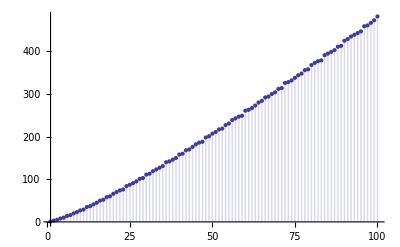

```mathematica
DiscretePlot[s1[n,2],{n,1,100}]
```

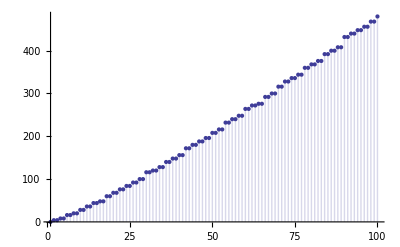

```mathematica
DiscretePlot[s1[n,2]-s2[n,2],{n,1,100}]
```

```mathematica
f[n_]:=(s1[2 n,2]-s2[2 n,2])/4
```

```mathematica
Table[{n,s2[n,1], s1[n,1]-2s1[Floor[n/2],1]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 0 | 0
3 | 1 | 1
4 | 0 | 0
5 | 1 | 1
6 | 0 | 0
7 | 1 | 1
8 | 0 | 0
9 | 1 | 1
10 | 0 | 0
11 | 1 | 1
12 | 0 | 0
13 | 1 | 1
14 | 0 | 0
15 | 1 | 1
16 | 0 | 0
17 | 1 | 1
18 | 0 | 0
19 | 1 | 1
20 | 0 | 0
21 | 1 | 1
22 | 0 | 0
23 | 1 | 1
24 | 0 | 0
25 | 1 | 1
26 | 0 | 0
27 | 1 | 1
28 | 0 | 0
29 | 1 | 1
30 | 0 | 0
31 | 1 | 1
32 | 0 | 0
33 | 1 | 1
34 | 0 | 0
35 | 1 | 1
36 | 0 | 0
37 | 1 | 1
38 | 0 | 0
39 | 1 | 1
40 | 0 | 0
41 | 1 | 1
42 | 0 | 0
43 | 1 | 1
44 | 0 | 0
45 | 1 | 1
46 | 0 | 0
47 | 1 | 1
48 | 0 | 0
49 | 1 | 1
50 | 0 | 0
51 | 1 | 1
52 | 0 | 0
53 | 1 | 1
54 | 0 | 0
55 | 1 | 1
56 | 0 | 0
57 | 1 | 1
58 | 0 | 0
59 | 1 | 1
60 | 0 | 0
61 | 1 | 1
62 | 0 | 0
63 | 1 | 1
64 | 0 | 0
65 | 1 | 1
66 | 0 | 0
67 | 1 | 1
68 | 0 | 0
69 | 1 | 1
70 | 0 | 0
71 | 1 | 1
72 | 0 | 0
73 | 1 | 1
74 | 0 | 0
75 | 1 | 1
76 | 0 | 0
77 | 1 | 1
78 | 0 | 0
79 | 1 | 1
80 | 0 | 0
81 | 1 | 1
82 | 0 | 0
83 | 1 | 1
84 | 0 | 0
85 | 1 | 1
86 | 0 | 0
87 | 1 | 1
88 | 0 | 0
89 | 1 | 1
90 | 0 | 0
91 | 1 | 1
92 | 0 | 0
93 | 1 | 1
94 | 0 | 0
95 | 1 | 1
96 | 0 | 0
97 | 1 | 1
98 | 0 | 0
99 | 1 | 1
100 | 0 | 0

```mathematica
Table[{n,s2[n,2], s1[n,2]-4 s1[Floor[n/2],2] + 4 s1[Floor[n/4],2]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | -1 | -1
3 | 1 | 1
4 | 0 | 0
5 | 2 | 2
6 | -2 | -2
7 | 0 | 0
8 | 0 | 0
9 | 3 | 3
10 | -1 | -1
11 | 1 | 1
12 | -1 | -1
13 | 1 | 1
14 | -3 | -3
15 | 1 | 1
16 | 2 | 2
17 | 4 | 4
18 | -2 | -2
19 | 0 | 0
20 | -2 | -2
21 | 2 | 2
22 | -2 | -2
23 | 0 | 0
24 | 0 | 0
25 | 3 | 3
26 | -1 | -1
27 | 3 | 3
28 | 1 | 1
29 | 3 | 3
30 | -5 | -5
31 | -3 | -3
32 | -1 | -1
33 | 3 | 3
34 | -1 | -1
35 | 3 | 3
36 | 0 | 0
37 | 2 | 2
38 | -2 | -2
39 | 2 | 2
40 | 2 | 2
41 | 4 | 4
42 | -4 | -4
43 | -2 | -2
44 | -4 | -4
45 | 2 | 2
46 | -2 | -2
47 | 0 | 0
48 | 2 | 2
49 | 5 | 5
50 | -1 | -1
51 | 3 | 3
52 | 1 | 1
53 | 3 | 3
54 | -5 | -5
55 | -1 | -1
56 | -1 | -1
57 | 3 | 3
58 | -1 | -1
59 | 1 | 1
60 | -3 | -3
61 | -1 | -1
62 | -5 | -5
63 | 1 | 1
64 | 4 | 4
65 | 8 | 8
66 | 0 | 0
67 | 2 | 2
68 | 0 | 0
69 | 4 | 4
70 | -4 | -4
71 | -2 | -2
72 | -2 | -2
73 | 0 | 0
74 | -4 | -4
75 | 2 | 2
76 | 0 | 0
77 | 4 | 4
78 | -4 | -4
79 | -2 | -2
80 | 0 | 0
81 | 5 | 5
82 | 1 | 1
83 | 3 | 3
84 | -1 | -1
85 | 3 | 3
86 | -1 | -1
87 | 3 | 3
88 | 3 | 3
89 | 5 | 5
90 | -7 | -7
91 | -3 | -3
92 | -5 | -5
93 | -1 | -1
94 | -5 | -5
95 | -1 | -1
96 | 3 | 3
97 | 5 | 5
98 | -1 | -1
99 | 5 | 5
100 | 2 | 2

```mathematica
Expand[(x-2)^3]
```

-8+12 x-6 x^2+x^3

```mathematica
Table[{n,s2[n,3], s1[n,3]-6 s1[Floor[n/2],3] + 12 s1[Floor[n/4],3]-8 s1[Floor[n/8],3]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | -2 | -2
3 | 1 | 1
4 | 1 | 1
5 | 4 | 4
6 | -5 | -5
7 | -2 | -2
8 | 0 | 0
9 | 6 | 6
10 | -3 | -3
11 | 0 | 0
12 | 0 | 0
13 | 3 | 3
14 | -6 | -6
15 | 3 | 3
16 | 6 | 6
17 | 9 | 9
18 | -9 | -9
19 | -6 | -6
20 | -6 | -6
21 | 3 | 3
22 | -6 | -6
23 | -3 | -3
24 | 3 | 3
25 | 9 | 9
26 | 0 | 0
27 | 10 | 10
28 | 10 | 10
29 | 13 | 13
30 | -14 | -14
31 | -11 | -11
32 | -8 | -8
33 | 1 | 1
34 | -8 | -8
35 | 1 | 1
36 | 1 | 1
37 | 4 | 4
38 | -5 | -5
39 | 4 | 4
40 | 10 | 10
41 | 13 | 13
42 | -14 | -14
43 | -11 | -11
44 | -11 | -11
45 | 7 | 7
46 | -2 | -2
47 | 1 | 1
48 | 10 | 10
49 | 16 | 16
50 | -2 | -2
51 | 7 | 7
52 | 7 | 7
53 | 10 | 10
54 | -20 | -20
55 | -11 | -11
56 | -5 | -5
57 | 4 | 4
58 | -5 | -5
59 | -2 | -2
60 | -2 | -2
61 | 1 | 1
62 | -8 | -8
63 | 10 | 10
64 | 12 | 12
65 | 21 | 21
66 | -6 | -6
67 | -3 | -3
68 | -3 | -3
69 | 6 | 6
70 | -21 | -21
71 | -18 | -18
72 | -6 | -6
73 | -3 | -3
74 | -12 | -12
75 | 6 | 6
76 | 6 | 6
77 | 15 | 15
78 | -12 | -12
79 | -9 | -9
80 | 0 | 0
81 | 15 | 15
82 | 6 | 6
83 | 9 | 9
84 | 9 | 9
85 | 18 | 18
86 | 9 | 9
87 | 18 | 18
88 | 24 | 24
89 | 27 | 27
90 | -27 | -27
91 | -18 | -18
92 | -18 | -18
93 | -9 | -9
94 | -18 | -18
95 | -9 | -9
96 | 0 | 0
97 | 3 | 3
98 | -15 | -15
99 | 3 | 3
100 | 3 | 3

```mathematica
Expand[(x-2)^4]
```

16-32 x+24 x^2-8 x^3+x^4

```mathematica
Table[{n,s2[n,4], s1[n,4]-8 s1[Floor[n/2],4] + 24 s1[Floor[n/4],4]-32 s1[Floor[n/8],4]+16 s1[Floor[n/16],4]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | -3 | -3
3 | 1 | 1
4 | 3 | 3
5 | 7 | 7
6 | -9 | -9
7 | -5 | -5
8 | -1 | -1
9 | 9 | 9
10 | -7 | -7
11 | -3 | -3
12 | 5 | 5
13 | 9 | 9
14 | -7 | -7
15 | 9 | 9
16 | 12 | 12
17 | 16 | 16
18 | -24 | -24
19 | -20 | -20
20 | -12 | -12
21 | 4 | 4
22 | -12 | -12
23 | -8 | -8
24 | 8 | 8
25 | 18 | 18
26 | 2 | 2
27 | 22 | 22
28 | 30 | 30
29 | 34 | 34
30 | -30 | -30
31 | -26 | -26
32 | -26 | -26
33 | -10 | -10
34 | -26 | -26
35 | -10 | -10
36 | 10 | 10
37 | 14 | 14
38 | -2 | -2
39 | 14 | 14
40 | 30 | 30
41 | 34 | 34
42 | -30 | -30
43 | -26 | -26
44 | -18 | -18
45 | 22 | 22
46 | 6 | 6
47 | 10 | 10
48 | 22 | 22
49 | 32 | 32
50 | -8 | -8
51 | 8 | 8
52 | 16 | 16
53 | 20 | 20
54 | -60 | -60
55 | -44 | -44
56 | -28 | -28
57 | -12 | -12
58 | -28 | -28
59 | -24 | -24
60 | 8 | 8
61 | 12 | 12
62 | -4 | -4
63 | 36 | 36
64 | 32 | 32
65 | 48 | 48
66 | -16 | -16
67 | -12 | -12
68 | -4 | -4
69 | 12 | 12
70 | -52 | -52
71 | -48 | -48
72 | -8 | -8
73 | -4 | -4
74 | -20 | -20
75 | 20 | 20
76 | 28 | 28
77 | 44 | 44
78 | -20 | -20
79 | -16 | -16
80 | -4 | -4
81 | 31 | 31
82 | 15 | 15
83 | 19 | 19
84 | 51 | 51
85 | 67 | 67
86 | 51 | 51
87 | 67 | 67
88 | 83 | 83
89 | 87 | 87
90 | -73 | -73
91 | -57 | -57
92 | -49 | -49
93 | -33 | -33
94 | -49 | -49
95 | -33 | -33
96 | -33 | -33
97 | -29 | -29
98 | -69 | -69
99 | -29 | -29
100 | -9 | -9

```mathematica
Table[{n,s1[n,1], Sum[ Binomial[k+0,0]2^k s2[ Floor[n/2^k],1],{k,0,Log[2,n]}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 2 | 2
3 | 3 | 3
4 | 4 | 4
5 | 5 | 5
6 | 6 | 6
7 | 7 | 7
8 | 8 | 8
9 | 9 | 9
10 | 10 | 10
11 | 11 | 11
12 | 12 | 12
13 | 13 | 13
14 | 14 | 14
15 | 15 | 15
16 | 16 | 16
17 | 17 | 17
18 | 18 | 18
19 | 19 | 19
20 | 20 | 20
21 | 21 | 21
22 | 22 | 22
23 | 23 | 23
24 | 24 | 24
25 | 25 | 25
26 | 26 | 26
27 | 27 | 27
28 | 28 | 28
29 | 29 | 29
30 | 30 | 30
31 | 31 | 31
32 | 32 | 32
33 | 33 | 33
34 | 34 | 34
35 | 35 | 35
36 | 36 | 36
37 | 37 | 37
38 | 38 | 38
39 | 39 | 39
40 | 40 | 40
41 | 41 | 41
42 | 42 | 42
43 | 43 | 43
44 | 44 | 44
45 | 45 | 45
46 | 46 | 46
47 | 47 | 47
48 | 48 | 48
49 | 49 | 49
50 | 50 | 50
51 | 51 | 51
52 | 52 | 52
53 | 53 | 53
54 | 54 | 54
55 | 55 | 55
56 | 56 | 56
57 | 57 | 57
58 | 58 | 58
59 | 59 | 59
60 | 60 | 60
61 | 61 | 61
62 | 62 | 62
63 | 63 | 63
64 | 64 | 64
65 | 65 | 65
66 | 66 | 66
67 | 67 | 67
68 | 68 | 68
69 | 69 | 69
70 | 70 | 70
71 | 71 | 71
72 | 72 | 72
73 | 73 | 73
74 | 74 | 74
75 | 75 | 75
76 | 76 | 76
77 | 77 | 77
78 | 78 | 78
79 | 79 | 79
80 | 80 | 80
81 | 81 | 81
82 | 82 | 82
83 | 83 | 83
84 | 84 | 84
85 | 85 | 85
86 | 86 | 86
87 | 87 | 87
88 | 88 | 88
89 | 89 | 89
90 | 90 | 90
91 | 91 | 91
92 | 92 | 92
93 | 93 | 93
94 | 94 | 94
95 | 95 | 95
96 | 96 | 96
97 | 97 | 97
98 | 98 | 98
99 | 99 | 99
100 | 100 | 100

```mathematica
Sum[ 2^k s2[ Floor[100/(2^k)],1],{k,0,Log[2,100]}]
```

100

```mathematica
Expand[(x^0+2x^1+4x^2+8x^3+16x^4+32x^5+64x^6+128x^7+256x^8+512x^9+1024x^10)^2]
```

1+4 x+12 x^2+32 x^3+80 x^4+192 x^5+448 x^6+1024 x^7+2304 x^8+5120 x^9+11264 x^10+20480 x^11+36864 x^12+65536 x^13+114688 x^14+196608 x^15+327680 x^16+524288 x^17+786432 x^18+1048576 x^19+1048576 x^20

```mathematica
ff[n_] := 2^(n-1) n
```

```mathematica
ff[5]
```

80

```mathematica
Table[{n,s1[n,2], Sum[ Binomial[k+1,1] 2^k s2[ Floor[n/2^k],2],{k,0,Log[2,n]}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 3 | 3
3 | 5 | 5
4 | 8 | 8
5 | 10 | 10
6 | 14 | 14
7 | 16 | 16
8 | 20 | 20
9 | 23 | 23
10 | 27 | 27
11 | 29 | 29
12 | 35 | 35
13 | 37 | 37
14 | 41 | 41
15 | 45 | 45
16 | 50 | 50
17 | 52 | 52
18 | 58 | 58
19 | 60 | 60
20 | 66 | 66
21 | 70 | 70
22 | 74 | 74
23 | 76 | 76
24 | 84 | 84
25 | 87 | 87
26 | 91 | 91
27 | 95 | 95
28 | 101 | 101
29 | 103 | 103
30 | 111 | 111
31 | 113 | 113
32 | 119 | 119
33 | 123 | 123
34 | 127 | 127
35 | 131 | 131
36 | 140 | 140
37 | 142 | 142
38 | 146 | 146
39 | 150 | 150
40 | 158 | 158
41 | 160 | 160
42 | 168 | 168
43 | 170 | 170
44 | 176 | 176
45 | 182 | 182
46 | 186 | 186
47 | 188 | 188
48 | 198 | 198
49 | 201 | 201
50 | 207 | 207
51 | 211 | 211
52 | 217 | 217
53 | 219 | 219
54 | 227 | 227
55 | 231 | 231
56 | 239 | 239
57 | 243 | 243
58 | 247 | 247
59 | 249 | 249
60 | 261 | 261
61 | 263 | 263
62 | 267 | 267
63 | 273 | 273
64 | 280 | 280
65 | 284 | 284
66 | 292 | 292
67 | 294 | 294
68 | 300 | 300
69 | 304 | 304
70 | 312 | 312
71 | 314 | 314
72 | 326 | 326
73 | 328 | 328
74 | 332 | 332
75 | 338 | 338
76 | 344 | 344
77 | 348 | 348
78 | 356 | 356
79 | 358 | 358
80 | 368 | 368
81 | 373 | 373
82 | 377 | 377
83 | 379 | 379
84 | 391 | 391
85 | 395 | 395
86 | 399 | 399
87 | 403 | 403
88 | 411 | 411
89 | 413 | 413
90 | 425 | 425
91 | 429 | 429
92 | 435 | 435
93 | 439 | 439
94 | 443 | 443
95 | 447 | 447
96 | 459 | 459
97 | 461 | 461
98 | 467 | 467
99 | 473 | 473
100 | 482 | 482

```mathematica
Expand[(x^0+2x^1+4x^2+8x^3+16x^4+32x^5+64x^6+128x^7+256x^8+512x^9+1024x^10)^3]
```

1+6 x+24 x^2+80 x^3+240 x^4+672 x^5+1792 x^6+4608 x^7+11520 x^8+28160 x^9+67584 x^10+153600 x^11+335872 x^12+712704 x^13+1474560 x^14+2981888 x^15+5898240 x^16+11403264 x^17+21495808 x^18+39321600 x^19+69206016 x^20+115343360 x^21+188743680 x^22+301989888 x^23+469762048 x^24+704643072 x^25+1006632960 x^26+1342177280 x^27+1610612736 x^28+1610612736 x^29+1073741824 x^30

```mathematica
Table[{n,s1[n,3], Sum[ Binomial[k+2,2] 2^k s2[ Floor[n/2^k],3],{k,0,Log[2,n]}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 4 | 4
3 | 7 | 7
4 | 13 | 13
5 | 16 | 16
6 | 25 | 25
7 | 28 | 28
8 | 38 | 38
9 | 44 | 44
10 | 53 | 53
11 | 56 | 56
12 | 74 | 74
13 | 77 | 77
14 | 86 | 86
15 | 95 | 95
16 | 110 | 110
17 | 113 | 113
18 | 131 | 131
19 | 134 | 134
20 | 152 | 152
21 | 161 | 161
22 | 170 | 170
23 | 173 | 173
24 | 203 | 203
25 | 209 | 209
26 | 218 | 218
27 | 228 | 228
28 | 246 | 246
29 | 249 | 249
30 | 276 | 276
31 | 279 | 279
32 | 300 | 300
33 | 309 | 309
34 | 318 | 318
35 | 327 | 327
36 | 363 | 363
37 | 366 | 366
38 | 375 | 375
39 | 384 | 384
40 | 414 | 414
41 | 417 | 417
42 | 444 | 444
43 | 447 | 447
44 | 465 | 465
45 | 483 | 483
46 | 492 | 492
47 | 495 | 495
48 | 540 | 540
49 | 546 | 546
50 | 564 | 564
51 | 573 | 573
52 | 591 | 591
53 | 594 | 594
54 | 624 | 624
55 | 633 | 633
56 | 663 | 663
57 | 672 | 672
58 | 681 | 681
59 | 684 | 684
60 | 738 | 738
61 | 741 | 741
62 | 750 | 750
63 | 768 | 768
64 | 796 | 796
65 | 805 | 805
66 | 832 | 832
67 | 835 | 835
68 | 853 | 853
69 | 862 | 862
70 | 889 | 889
71 | 892 | 892
72 | 952 | 952
73 | 955 | 955
74 | 964 | 964
75 | 982 | 982
76 | 1000 | 1000
77 | 1009 | 1009
78 | 1036 | 1036
79 | 1039 | 1039
80 | 1084 | 1084
81 | 1099 | 1099
82 | 1108 | 1108
83 | 1111 | 1111
84 | 1165 | 1165
85 | 1174 | 1174
86 | 1183 | 1183
87 | 1192 | 1192
88 | 1222 | 1222
89 | 1225 | 1225
90 | 1279 | 1279
91 | 1288 | 1288
92 | 1306 | 1306
93 | 1315 | 1315
94 | 1324 | 1324
95 | 1333 | 1333
96 | 1396 | 1396
97 | 1399 | 1399
98 | 1417 | 1417
99 | 1435 | 1435
100 | 1471 | 1471

```mathematica
Expand[(x^0+2x^1+4x^2+8x^3+16x^4+32x^5+64x^6+128x^7+256x^8+512x^9+1024x^10)^4]
```

1+8 x+40 x^2+160 x^3+560 x^4+1792 x^5+5376 x^6+15360 x^7+42240 x^8+112640 x^9+292864 x^10+737280 x^11+1798144 x^12+4259840 x^13+9830400 x^14+22151168 x^15+48824320 x^16+105381888 x^17+222822400 x^18+461373440 x^19+934281216 x^20+1845493760 x^21+3565158400 x^22+6744440832 x^23+12499025920 x^24+22682796032 x^25+40265318400 x^26+69793218560 x^27+117843165184 x^28+193273528320 x^29+307090161664 x^30+472446402560 x^31+708669603840 x^32+1030792151040 x^33+1443109011456 x^34+1924145348608 x^35+2405181685760 x^36+2748779069440 x^37+2748779069440 x^38+2199023255552 x^39+1099511627776 x^40

```mathematica
Table[{n,s1[n,4], Sum[ Binomial[k+3,3] 2^k s2[ Floor[n/2^k],4],{k,0,Log[2,n]}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 5 | 5
3 | 9 | 9
4 | 19 | 19
5 | 23 | 23
6 | 39 | 39
7 | 43 | 43
8 | 63 | 63
9 | 73 | 73
10 | 89 | 89
11 | 93 | 93
12 | 133 | 133
13 | 137 | 137
14 | 153 | 153
15 | 169 | 169
16 | 204 | 204
17 | 208 | 208
18 | 248 | 248
19 | 252 | 252
20 | 292 | 292
21 | 308 | 308
22 | 324 | 324
23 | 328 | 328
24 | 408 | 408
25 | 418 | 418
26 | 434 | 434
27 | 454 | 454
28 | 494 | 494
29 | 498 | 498
30 | 562 | 562
31 | 566 | 566
32 | 622 | 622
33 | 638 | 638
34 | 654 | 654
35 | 670 | 670
36 | 770 | 770
37 | 774 | 774
38 | 790 | 790
39 | 806 | 806
40 | 886 | 886
41 | 890 | 890
42 | 954 | 954
43 | 958 | 958
44 | 998 | 998
45 | 1038 | 1038
46 | 1054 | 1054
47 | 1058 | 1058
48 | 1198 | 1198
49 | 1208 | 1208
50 | 1248 | 1248
51 | 1264 | 1264
52 | 1304 | 1304
53 | 1308 | 1308
54 | 1388 | 1388
55 | 1404 | 1404
56 | 1484 | 1484
57 | 1500 | 1500
58 | 1516 | 1516
59 | 1520 | 1520
60 | 1680 | 1680
61 | 1684 | 1684
62 | 1700 | 1700
63 | 1740 | 1740
64 | 1824 | 1824
65 | 1840 | 1840
66 | 1904 | 1904
67 | 1908 | 1908
68 | 1948 | 1948
69 | 1964 | 1964
70 | 2028 | 2028
71 | 2032 | 2032
72 | 2232 | 2232
73 | 2236 | 2236
74 | 2252 | 2252
75 | 2292 | 2292
76 | 2332 | 2332
77 | 2348 | 2348
78 | 2412 | 2412
79 | 2416 | 2416
80 | 2556 | 2556
81 | 2591 | 2591
82 | 2607 | 2607
83 | 2611 | 2611
84 | 2771 | 2771
85 | 2787 | 2787
86 | 2803 | 2803
87 | 2819 | 2819
88 | 2899 | 2899
89 | 2903 | 2903
90 | 3063 | 3063
91 | 3079 | 3079
92 | 3119 | 3119
93 | 3135 | 3135
94 | 3151 | 3151
95 | 3167 | 3167
96 | 3391 | 3391
97 | 3395 | 3395
98 | 3435 | 3435
99 | 3475 | 3475
100 | 3575 | 3575

```mathematica
Expand[ (x-2)^4]
```

16-32 x+24 x^2-8 x^3+x^4

```mathematica
Sum[(-1)^j Binomial[4,j]2^j st[Floor[n/2^j],4],{j,0,4}]
```

16 st[Floor[n/16],4]-32 st[Floor[n/8],4]+24 st[Floor[n/4],4]-8 st[Floor[n/2],4]+st[Floor[n],4]

```mathematica
Table[{n,s2[n,4], s1[n,4]-8 s1[Floor[n/2],4] + 24 s1[Floor[n/4],4]-32 s1[Floor[n/8],4]+16 s1[Floor[n/16],4]},{n,1,100}]//TableForm
```

```mathematica
Table[{n,s2[n,4],  Sum[(-1)^j Binomial[4,j]2^j s1[Floor[n/2^j],4],{j,0,4}]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | -3 | -3
3 | 1 | 1
4 | 3 | 3
5 | 7 | 7
6 | -9 | -9
7 | -5 | -5
8 | -1 | -1
9 | 9 | 9
10 | -7 | -7
11 | -3 | -3
12 | 5 | 5
13 | 9 | 9
14 | -7 | -7
15 | 9 | 9
16 | 12 | 12
17 | 16 | 16
18 | -24 | -24
19 | -20 | -20
20 | -12 | -12
21 | 4 | 4
22 | -12 | -12
23 | -8 | -8
24 | 8 | 8
25 | 18 | 18
26 | 2 | 2
27 | 22 | 22
28 | 30 | 30
29 | 34 | 34
30 | -30 | -30
31 | -26 | -26
32 | -26 | -26
33 | -10 | -10
34 | -26 | -26
35 | -10 | -10
36 | 10 | 10
37 | 14 | 14
38 | -2 | -2
39 | 14 | 14
40 | 30 | 30
41 | 34 | 34
42 | -30 | -30
43 | -26 | -26
44 | -18 | -18
45 | 22 | 22
46 | 6 | 6
47 | 10 | 10
48 | 22 | 22
49 | 32 | 32
50 | -8 | -8
51 | 8 | 8
52 | 16 | 16
53 | 20 | 20
54 | -60 | -60
55 | -44 | -44
56 | -28 | -28
57 | -12 | -12
58 | -28 | -28
59 | -24 | -24
60 | 8 | 8
61 | 12 | 12
62 | -4 | -4
63 | 36 | 36
64 | 32 | 32
65 | 48 | 48
66 | -16 | -16
67 | -12 | -12
68 | -4 | -4
69 | 12 | 12
70 | -52 | -52
71 | -48 | -48
72 | -8 | -8
73 | -4 | -4
74 | -20 | -20
75 | 20 | 20
76 | 28 | 28
77 | 44 | 44
78 | -20 | -20
79 | -16 | -16
80 | -4 | -4
81 | 31 | 31
82 | 15 | 15
83 | 19 | 19
84 | 51 | 51
85 | 67 | 67
86 | 51 | 51
87 | 67 | 67
88 | 83 | 83
89 | 87 | 87
90 | -73 | -73
91 | -57 | -57
92 | -49 | -49
93 | -33 | -33
94 | -49 | -49
95 | -33 | -33
96 | -33 | -33
97 | -29 | -29
98 | -69 | -69
99 | -29 | -29
100 | -9 | -9